```mathematica
Population[r_,parg_:Automatic]:=
(
x=Table[n,{n,1,200}];
 x[[1]]=0.5;
For[n=2,n≤200,n++,x[[n]]=r*x[[n-1]]*(1-x[[n-1]])];
ListPlot[x,PlotRange->parg]
)
```

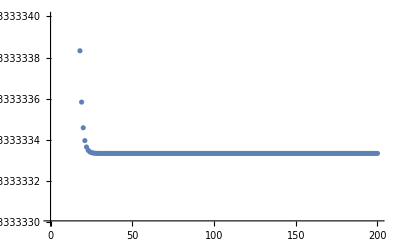

```mathematica
Population[1.5,{0.333333,0.333334}]
```

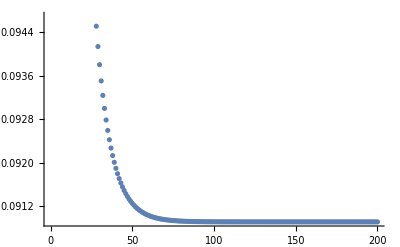

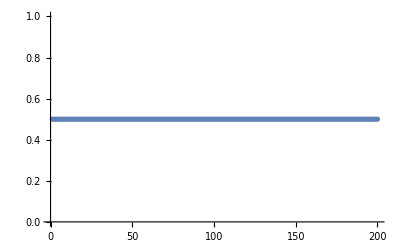

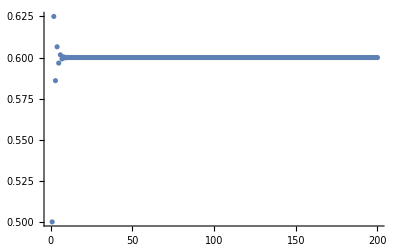

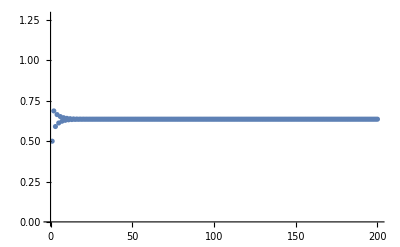

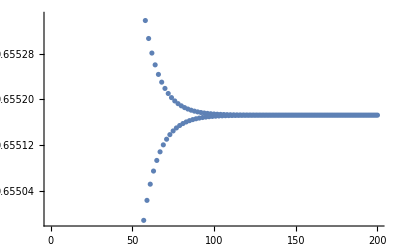

```mathematica
Population[1.1]
Population[2]
Population[2.5]
Population[2.75]
Population[2.9]
```

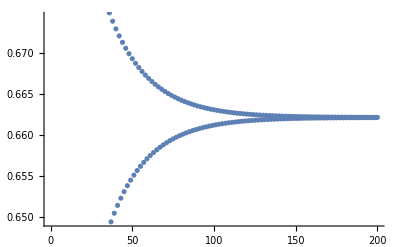

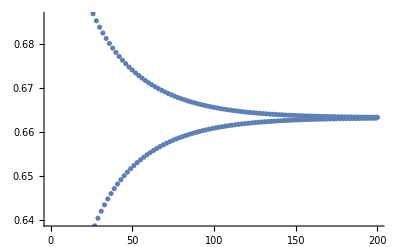

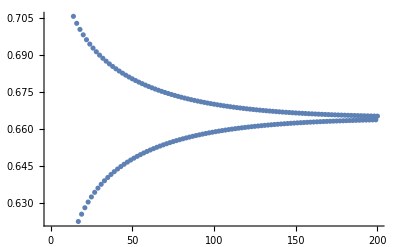

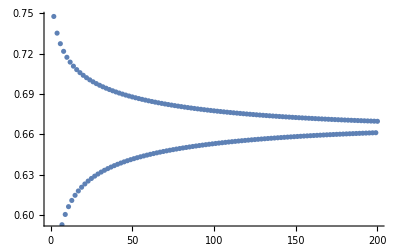

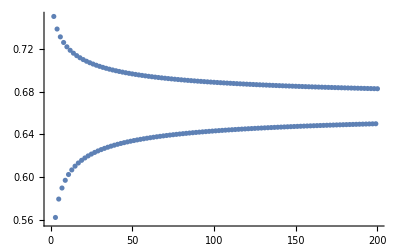

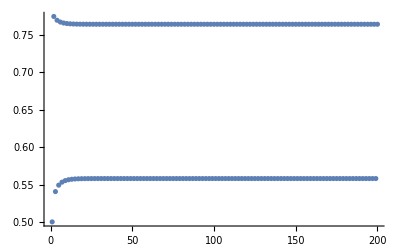

```mathematica
Population[2.96]
Population[2.97]
Population[2.98]
Population[2.99]
Population[3]
Population[3.1]
```

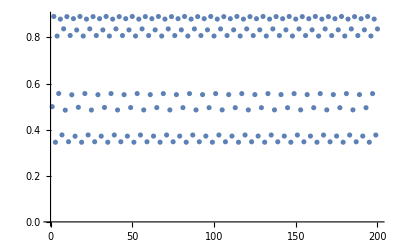

```mathematica
Population[3.565]
```